```mathematica
Задаём значения констант
```

```mathematica
ϵ=10^(-3);znak=4;κappa=1;w=0.5;
```

```mathematica
Определяем необходимые функции и точки спуска
```

```mathematica
X0={-1,-2};α=1;f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2
```

```mathematica
(*X0={-3,-2}; f[{x_,y_}]:=(x^2+y-11)^2+(x+y^2-7)^2
```

```mathematica
(*X0={0,0};X0={5,-5};X0={0,-4}; X0={-5,5};X0={-1,-2};X0={-3,-2};*)
```

```mathematica
(*X0={-2Sqrt[5],1};f[{x_,y_}]=6x^2+3y^2-4x y+4Sqrt[5](x+2y)+22;
```

```mathematica
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
```

```mathematica
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
```

```mathematica
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
```

```mathematica
Инициализируем переменные
```

```mathematica
i=0;
iArgMin={i};
symi=0;
X=X0;
points={X0};
norm={NormGradF[X0]};
κArray={κappa};fValues={f[X0]};
```

```mathematica
АЛГОРИТМ
```

```mathematica
While[norm[[-1]]≥ϵ,
(*наискорейший спуск*)
i:=0;
κArray=Append[κArray,NArgMin[f[X+κ antiGradF[X]],κ,StepMonitor:>i++]];
X+=κArray[[-1]] antiGradF[X];
points=Append[points,X];
fValues=Append[fValues,f[X]];i++;
symi+=i;
iArgMin=Append[iArgMin,i];
norm=Append[norm,NormGradF[X]];

(*дробление шага*)
(*X=points[[-1]];
κArray[[-1]]=κArray[[-1]] w;
X+=κArray[[-1]] antiGradF[X];
While[(f[X]-fValues[[-1]]≤w* ((norm[[-1]])^2)*κArray[[-1]]) && (norm[[-1]]≥ϵ), symi++;
κArray=Append[κArray,κArray[[-1]]];
norm=Append[norm,NormGradF[X]];
points=Append[points,X];
fValues=Append[fValues,f[X]]; symi++;
X+=κArray[[-1]] antiGradF[X];
]
symi++;*)
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: точка минимума X = "<>ToString[SetAccuracy[X,znak]]<>" Функция f(x) в алгоритме была вычислена "<>ToString[symi]<>" раз."
```

Результат получен за 97 итер.: точка минимума X = {0.999, 0.998} Функция f(x) в алгоритме была вычислена 5556 раз.

```mathematica
SetAccuracy[f[X],znak]" - минимум функции f(X)"
```

0.  - минимум функции f(X)

```mathematica
АНАЛИЗ РЕЗУЛЬТАТОВ ВЫЧИСЛИТЕЛЬНОГО ЭКСПЕРИМЕНТА
```

```mathematica
2. Траектория поиска точки минимума
```

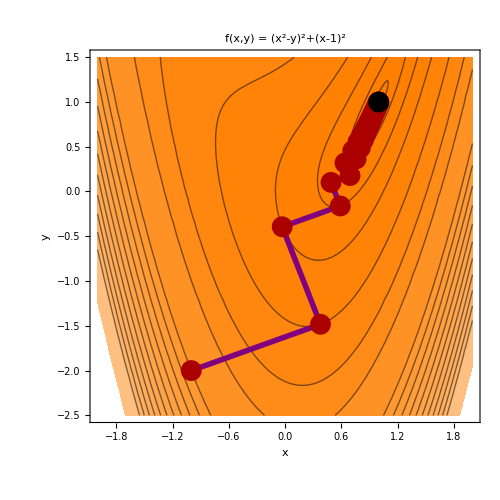

```mathematica
CP0={-2,-2.5}; CP1={2,1.5}; b:=20;
(*наискорейший спуск*)
(*CP0={-0.5,-0.5};CP1={4,4}; b:=20;функция Химмельблау а)*) 
(*CP0={2,-5.5};CP1={6,-1.5}; b:=20;функция Химмельблау б)*) 
(*CP0={-4,-4.5};CP1={4,3.5}; b:=9;функция Химмельблау в)*) 
(*CP0={-5.5,3};CP1={-2,5.5}; b:=10;функция Химмельблау г)*) 
(*CP0={-1.5,-2.5};CP1={4,3}; b:=13;функция Химмельблау д)*) 
(*CP0={-5,-4};CP1={-2.5,-1.5}; b:=13;функция Химмельблау е)*) 
(*CP0={-5,-5}; CP1={2,2}; b:=9; Квадратичная функция*) 
(*CP0={-3,-3}; CP1={3,3}; b:=20; функция Розенброка при лямда=1*)
(*CP0={-2,-2.5}; CP1={2,1.5}; b:=20; функция Розенброка при лямда=50*)

(*дробление шага*)
(*CP0={-5,-5}; CP1={2,2}; b:=20; Квадратичная функция*) 
(*CP0={-3,-3}; CP1={3,3}; b:=20; функция Розенброка при лямда=1*)
(*CP0={-2,-2.5}; CP1={2,1.5}; b:=20; функция Розенброка при лямда=50*)
ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[Length[points]]]]}]
```

```mathematica
3. Анализ сходимости метода: убывание нормы невязки
```

```mathematica
График убывания нормы невязки  в логарифмическом масштабе
```

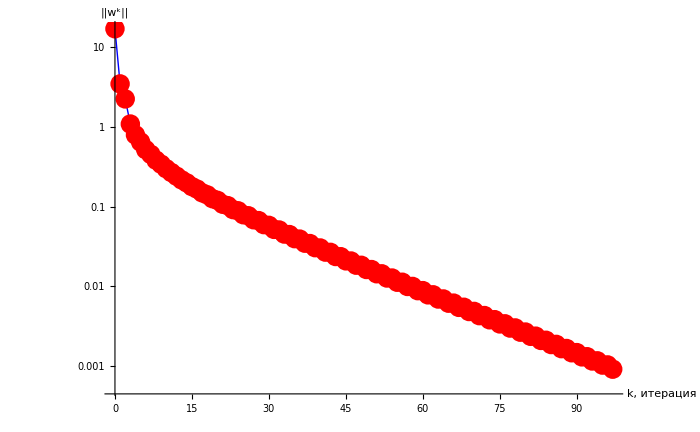

```mathematica
ListLogPlot[norm,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->700,Joined->True,Mesh->Full,DataRange->{0,Length[points]-1},MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||","i"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],znak]]<>", "<>ToString[SetAccuracy[points[[i,2]],znak]]<>" )"]
gridData[[All,3]]=SetAccuracy[fValues,znak];
gridData[[All,4]]=SetAccuracy[κArray,znak];
gridData[[All,5]]=SetAccuracy[norm,znak];
gridData[[All,6]]=iArgMin;
gridData={gridLabel}~Join~gridData;
```

```mathematica
Grid[gridData[[1;;10]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[Length[points]-4;;Length[points]+1]],Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
(*Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]*)
```

k | X^k | f(X^k) | κ_k | ||w^k|| | i
0 | ( -1.000, -2.000 ) | 13. | 1. | 17.09 | 0
1 | ( 0.379, -1.483 ) | 3.031 | 0.086 | 3.474 | 65
2 | ( -0.030, -0.394 ) | 1.216 | 0.335 | 2.25 | 55
3 | ( 0.590, -0.162 ) | 0.428 | 0.294 | 1.089 | 73
4 | ( 0.491, 0.102 ) | 0.278 | 0.258 | 0.794 | 65
5 | ( 0.693, 0.178 ) | 0.186 | 0.272 | 0.648 | 65
6 | ( 0.640, 0.319 ) | 0.138 | 0.233 | 0.519 | 65
7 | ( 0.758, 0.363 ) | 0.103 | 0.243 | 0.452 | 65
8 | ( 0.723, 0.456 ) | 0.081 | 0.219 | 0.383 | 55
... | ... | ... | ... | ... | ...
92 | ( 0.999, 0.998 ) | 0. | 0.178 | 0.001 | 64
93 | ( 0.999, 0.998 ) | 0. | 0.157 | 0.001 | 64
94 | ( 0.999, 0.998 ) | 0. | 0.178 | 0.001 | 64
95 | ( 0.999, 0.998 ) | 0. | 0.157 | 0.001 | 54
96 | ( 0.999, 0.998 ) | 0. | 0.178 | 0.001 | 54
97 | ( 0.999, 0.998 ) | 0. | 0.157 | 0.0009 | 54